```mathematica
DATA = Import["/home/hardik/Desktop/MTech_Project/Scripts/Mathematica/Feature.mat","LabeledData"]
```

{trainData→{{0.250944,0.263878,0.235256,0.326701,0.362273,0.454085,0.212602,0.372437,0.368494},88378,{0.452277,7,0.49539}},2,trainLabel→1}
 |  |  |  |

```mathematica
Dimensions[DATA[["trainLabel"]]]
```

{}

```mathematica
training = DATA[[1]][[2]]
```

{{0.250944,0.263878,0.235256,0.326701,0.362273,0.454085,0.212602,0.372437,0.368494},88378,{0.452277,0.440577,5,0.44044,0.49539}}
 |  |  |  |

```mathematica
Dimensions[training]
```

{88380,9}

```mathematica
trainLabel = Flatten[DATA[[4]][[2]]+1]
```

{1,6,2,2,5,3,5,2,6,6,5,2,2,2,2,6,6,2,2,6,5,6,3,4,3,3,4,3,3,2,5,4,6,1,2,3,6,3,6,6,3,3,6,2,5,3,4,1,5,4,2,6,2,1,3,3,2,3,6,5,2,3,3,2,6,5,6,6,5,2,6,6,2,88234,4,6,5,2,2,5,3,5,5,3,2,2,6,1,2,3,3,5,2,6,1,3,2,6,2,2,6,2,2,3,3,3,4,3,2,2,3,2,2,4,1,3,4,5,2,5,2,2,2,2,5,4,4,4,6,5,6,3,6,4,5,2,2,2,6,6,4,5,2,5,6,3,2}
 |  |  |  |

```mathematica
Dimensions[trainLabel]
```

{88380}

```mathematica
testing = DATA[[3][[2]]]
```

```mathematica
Dimensions[testing]
```

{9820,9}

```mathematica
testLabel =Flatten[ DATA[[2]][[2]]+1]
```

{3,2,6,6,2,1,5,3,4,2,5,3,3,6,2,4,3,5,4,3,1,2,4,1,2,2,6,5,3,4,3,5,3,2,6,2,5,5,5,2,6,3,1,2,5,2,4,3,5,2,5,1,6,2,3,5,3,2,5,2,2,4,5,2,5,3,3,3,3,5,5,2,5,4,4,5,2,2,2,2,5,2,1,2,1,1,6,5,4,3,4,2,6,1,6,4,2,6,4,2,4,2,4,5,6,5,3,2,3,3,6,2,2,3,1,2,3,2,2,6,2,2,4,3,2,5,5,6,3,2,2,3,2,4,2,3,2,5,5,2,2,3,2,6,5,5,3,3,3,2,3,2,2,2,2,2,5,2,5,2,5,2,2,5,5,5,5,2,2,1,1,2,3,5,6,3,2,4,3,6,6,4,5,3,5,2,4,2,6,2,5,1,2,2,4,3,4,3,6,2,4,6,6,4,2,5,2,2,5,2,6,3,2,6,4,2,6,2,5,3,6,2,3,3,2,3,6,3,5,2,2,2,2,3,2,5,6,5,6,5,5,4,4,2,2,2,2,3,2,1,6,6,1,2,3,2,2,6,3,2,2,5,2,3,2,6,6,2,5,6,2,6,5,2,6,4,3,6,5,2,5,6,6,2,3,2,3,2,2,6,3,4,2,2,3,3,6,6,4,3,3,4,5,1,2,2,6,6,1,5,6,2,5,2,4,2,1,5,5,3,5,5,6,1,5,2,3,3,5,2,2,2,5,3,2,3,5,2,6,6,2,6,6,5,6,6,4,6,3,4,4,6,3,6,2,2,4,2,2,2,5,5,5,2,3,6,4,4,2,5,4,1,2,5,5,2,6,2,2,3,5,6,2,6,2,2,6,5,2,4,2,6,5,3,6,2,6,5,1,5,5,2,2,2,3,1,5,2,2,3,2,6,1,4,6,3,6,2,3,2,1,3,2,1,2,6,3,6,6,2,6,2,4,2,2,2,3,2,3,1,2,5,2,2,5,6,3,3,3,2,4,6,3,5,3,3,2,2,4,5,2,2,4,2,1,5,3,3,6,5,4,6,5,2,4,2,6,5,2,6,5,2,3,3,5,2,5,5,6,4,2,2,5,2,3,1,2,1,3,4,2,1,3,2,2,3,6,3,5,6,6,3,6,3,3,2,2,2,4,2,4,5,2,3,5,2,4,4,2,3,2,2,2,2,3,2,2,2,2,3,2,4,4,6,5,6,5,4,4,2,5,3,6,6,2,6,6,6,2,2,3,3,6,6,2,3,2,6,3,6,2,3,5,6,2,2,6,5,2,3,5,5,6,4,4,1,2,5,6,6,4,1,6,3,5,3,2,4,6,6,2,2,2,2,5,2,3,5,5,2,1,2,2,2,3,2,1,5,1,4,5,6,6,3,6,3,2,2,6,1,5,4,5,2,2,5,3,1,2,5,6,2,1,2,2,3,2,5,3,2,2,2,5,6,3,1,2,3,4,6,2,4,2,2,6,2,3,6,6,2,6,6,6,4,2,2,2,2,6,6,1,5,2,2,5,3,2,4,6,5,5,2,4,3,3,6,3,2,6,5,4,4,2,6,1,2,3,3,6,6,6,3,4,5,2,5,4,6,6,3,2,3,5,2,2,6,5,2,4,3,3,3,3,3,6,6,2,4,4,2,2,3,6,2,2,3,5,3,3,6,2,3,2,4,4,2,3,4,2,2,3,5,3,1,5,1,2,2,3,4,6,2,6,2,2,2,3,2,2,3,2,3,5,2,2,3,5,2,2,3,5,2,5,5,3,5,1,5,6,5,1,4,3,1,2,3,3,1,2,4,6,4,3,1,4,3,5,6,3,6,6,4,3,2,2,5,2,2,3,5,3,4,6,3,1,5,5,2,6,5,1,5,1,2,2,6,6,6,4,1,2,4,6,6,3,5,5,6,4,3,6,2,2,1,3,5,3,2,2,1,6,5,6,2,2,3,6,5,2,4,4,2,1,6,3,5,2,3,2,5,6,5,2,3,5,5,2,6,5,2,6,6,1,4,5,3,2,3,6,6,2,6,2,2,6,2,5,4,2,3,6,5,1,4,2,5,4,5,1,5,5,5,2,3,6,3,2,6,4,4,4,5,6,6,4,3,2,6,3,2,4,6,2,5,6,2,3,1,4,6,2,4,1,3,5,5,3,6,2,3,3,1,2,3,2,2,6,6,3,5,5,6,3,4,6,5,2,1,5,5,3,6,4,2,2,1,5,6,5,5,6,1,3,2,3,3,5,3,5,2,3,5,5,2,2,4,6,2,3,2,4,1,5,2,2,2,3,3,1,6,2,4,5,5,6,5,6,2,2,5,6,2,5,5,2,1,2,1,1,3,2,5,2,1,4,5,2,2,6,3,2,6,4,2,2,3,6,6,4,1,5,3,4,1,6,3,2,2,2,2,3,3,2,3,6,6,6,6,3,6,5,6,5,2,3,3,5,5,3,2,3,6,5,6,2,5,2,4,6,2,5,3,2,3,3,2,6,2,2,2,6,2,2,3,2,5,6,3,3,3,5,3,3,2,3,1,6,2,4,5,3,4,6,2,2,2,2,3,5,2,3,2,4,2,5,2,3,1,5,4,2,2,3,3,4,2,2,1,2,5,5,2,5,5,5,6,2,5,5,2,5,5,2,5,6,3,6,2,4,6,3,3,1,5,6,6,2,4,6,3,3,1,5,3,2,6,1,4,1,6,1,4,1,4,2,6,2,2,2,2,5,2,2,4,4,3,1,2,5,5,4,6,3,2,6,5,2,6,3,3,2,2,5,5,3,5,3,2,2,3,2,2,5,2,6,4,2,1,3,5,2,3,5,1,4,6,2,2,5,3,3,3,2,6,5,3,5,5,3,5,5,4,4,2,5,6,6,6,5,3,4,1,4,2,4,5,4,2,2,2,5,6,2,2,5,2,6,6,2,3,3,2,5,3,5,4,3,5,6,2,5,5,4,5,3,4,2,2,5,2,2,6,4,1,4,5,3,4,3,6,3,6,3,3,3,2,6,3,3,6,1,2,2,2,2,6,3,5,2,2,5,2,5,5,5,5,2,2,5,5,4,2,2,3,2,5,1,2,2,5,4,2,4,3,6,3,2,4,2,5,6,3,1,2,5,6,6,6,5,2,4,1,6,6,1,2,5,3,2,2,2,2,3,2,4,5,3,5,4,2,5,6,2,5,5,3,5,1,5,2,2,3,3,3,3,5,5,2,5,4,4,2,1,3,1,4,6,1,6,3,5,3,2,2,6,1,1,6,6,5,3,5,3,2,6,5,3,3,6,5,4,2,4,3,2,3,6,2,5,6,3,6,2,4,6,3,3,3,2,2,6,1,2,3,1,4,3,3,4,2,2,5,4,1,6,2,6,3,3,5,3,3,3,5,2,4,3,6,6,2,4,2,5,2,3,6,2,1,5,2,3,3,1,2,6,3,6,3,3,2,2,4,6,4,2,6,1,4,3,2,1,5,5,5,2,3,6,2,3,4,3,5,2,3,6,4,2,4,5,2,2,3,5,6,2,4,3,2,6,6,2,5,2,2,6,3,3,5,4,1,1,3,3,5,1,6,2,2,2,3,2,5,3,2,5,5,6,2,4,5,2,3,5,3,3,6,5,2,5,3,3,3,3,4,1,5,4,3,3,3,3,6,1,3,3,5,4,6,2,2,3,5,2,2,3,2,5,3,2,2,6,3,1,6,6,4,3,2,6,1,5,2,6,2,4,6,1,3,2,4,3,5,2,1,3,5,2,1,2,5,2,6,4,2,5,5,2,6,3,2,6,2,5,6,3,3,2,2,6,6,2,3,6,2,5,2,2,3,3,6,2,1,5,3,4,2,3,2,4,3,2,5,6,5,2,5,5,2,2,6,2,1,6,2,5,6,6,4,3,5,1,5,6,5,6,2,5,2,6,5,3,3,5,1,6,4,5,2,3,3,6,5,2,2,2,6,1,5,3,2,3,2,5,2,2,4,4,6,2,2,2,2,2,6,1,6,2,5,3,3,5,2,5,6,2,5,2,5,2,1,3,6,5,2,3,4,4,2,6,6,5,4,6,1,5,6,6,2,3,3,4,2,3,5,3,3,2,1,2,3,3,2,6,1,5,4,2,3,1,2,6,3,4,5,2,6,2,5,1,3,5,1,2,6,6,2,6,2,4,2,4,6,5,6,2,4,5,2,3,6,6,2,4,4,3,6,2,4,2,2,6,2,3,1,3,6,4,6,2,3,6,6,3,2,6,2,1,6,2,2,5,2,2,5,2,6,2,6,6,6,2,3,2,3,5,3,5,5,4,2,3,4,4,6,4,5,6,3,5,6,4,4,4,5,3,4,4,5,6,2,2,5,6,1,3,6,5,6,5,6,6,2,1,5,5,5,5,3,2,2,1,2,2,5,6,5,2,3,1,6,5,2,2,2,4,4,5,2,3,2,2,2,1,2,2,6,6,3,6,3,3,2,5,1,3,6,2,2,6,2,3,5,5,3,2,4,3,4,2,6,4,5,5,5,2,1,6,1,4,6,5,4,3,5,2,5,5,6,5,3,3,4,5,6,2,5,2,4,5,4,3,4,1,3,2,2,6,6,2,2,2,5,5,5,2,5,3,5,5,2,3,4,6,2,2,2,3,4,6,6,2,2,6,5,2,2,2,6,2,4,2,1,2,3,3,2,4,2,2,5,3,2,1,2,5,6,2,3,4,5,3,6,3,3,3,5,6,2,3,3,2,1,2,2,6,5,6,4,6,4,4,6,3,6,5,2,3,6,2,6,5,6,1,3,1,5,2,3,2,6,2,3,2,2,2,2,2,2,1,4,5,6,3,6,5,2,3,6,4,1,4,3,2,6,4,3,2,6,3,4,3,2,1,3,2,1,5,2,3,5,5,3,2,5,6,2,2,6,5,2,5,1,2,2,2,6,3,5,2,2,2,6,3,6,5,3,1,5,2,6,2,3,6,5,4,5,2,6,1,3,5,6,3,5,2,4,4,5,3,3,1,2,2,4,2,6,4,3,2,1,3,6,4,6,5,6,5,3,2,3,6,5,2,2,2,6,6,5,1,4,3,2,6,1,5,2,5,2,3,4,6,5,6,2,3,1,1,2,3,4,1,6,4,2,3,6,2,6,5,5,4,4,3,4,2,1,5,6,6,1,6,3,2,2,2,4,5,5,2,2,5,3,2,5,6,1,2,2,4,6,2,1,5,3,3,6,6,3,6,6,2,5,2,2,2,2,2,3,3,5,6,5,3,5,5,2,2,2,3,2,2,2,3,2,3,6,3,4,5,4,1,5,1,3,1,5,5,6,5,5,6,5,1,3,3,5,6,2,2,5,3,3,6,2,4,2,2,6,2,5,2,6,6,2,2,3,3,5,5,2,1,2,3,5,3,3,2,4,1,2,5,6,6,2,6,1,1,2,2,2,4,5,6,2,2,5,4,3,2,3,2,4,4,3,2,2,2,3,5,4,3,5,5,6,1,4,2,6,5,2,2,6,2,5,2,3,3,5,2,4,1,3,2,2,4,5,3,4,5,2,5,1,5,5,3,5,1,6,5,2,6,5,3,6,3,6,2,2,5,2,6,3,2,3,6,6,4,2,2,6,3,4,5,2,5,3,4,3,2,2,2,6,2,6,6,5,6,6,3,2,3,6,2,6,2,2,6,5,5,6,2,2,6,5,1,1,6,3,4,2,5,4,5,6,4,2,3,2,2,2,3,2,2,3,6,2,2,2,2,3,2,3,6,1,2,6,5,3,4,5,2,6,2,6,4,5,3,2,5,6,5,4,6,2,3,3,5,3,4,5,3,2,2,2,3,3,5,3,3,5,3,3,5,3,5,5,6,5,2,1,2,6,3,2,3,3,6,2,6,2,2,3,2,3,6,3,5,2,2,2,6,2,3,2,6,2,5,4,2,5,3,2,2,2,5,6,2,4,3,2,2,6,5,3,2,3,6,4,2,2,2,1,2,1,5,5,3,2,4,1,2,6,2,5,4,3,2,3,6,1,3,2,3,1,3,5,6,2,2,6,4,4,5,5,2,5,3,4,4,1,2,3,4,2,2,6,4,6,2,5,5,3,2,4,3,2,4,2,6,2,5,3,5,3,2,3,2,6,2,5,2,3,3,5,4,3,3,5,2,5,4,2,4,6,3,6,6,1,1,2,6,2,5,3,5,2,3,2,6,2,6,2,6,5,6,3,2,5,3,4,5,2,6,1,5,6,2,4,5,3,2,3,3,3,2,2,2,5,2,6,2,2,4,6,6,6,5,2,5,6,3,3,4,2,5,3,4,5,2,6,1,2,3,2,2,6,3,5,3,5,3,4,3,3,2,2,6,3,2,3,6,5,2,2,6,5,6,2,2,5,1,4,2,3,2,5,4,3,3,2,2,2,6,3,2,2,2,6,1,2,2,5,3,1,2,2,2,6,5,4,6,2,2,6,5,3,2,5,4,3,2,3,6,1,2,3,2,4,4,1,2,2,5,2,6,3,4,2,6,2,1,3,6,2,5,1,3,6,5,2,6,2,3,5,4,2,2,5,3,3,5,5,2,1,5,6,2,3,2,3,4,6,5,5,5,2,2,2,2,5,5,2,5,6,5,5,6,6,2,1,5,2,2,6,6,3,2,4,6,1,5,4,2,2,1,6,3,2,5,2,2,5,6,2,3,2,3,4,3,6,5,2,3,1,6,2,6,2,3,2,2,6,2,3,5,4,1,3,2,3,4,2,5,2,6,2,1,4,1,6,1,2,5,4,5,5,2,1,1,3,2,2,6,3,5,3,2,5,6,5,1,6,3,6,3,3,3,2,4,5,2,4,2,5,3,3,2,2,2,6,4,3,2,1,6,1,6,1,4,4,4,2,1,6,2,3,3,3,2,5,2,5,4,5,3,4,2,2,5,6,2,4,3,1,2,6,2,2,2,6,2,1,2,4,2,2,2,2,4,2,4,2,3,3,2,2,3,3,6,5,2,3,2,3,3,6,2,2,6,4,4,6,3,6,6,1,2,6,2,5,5,5,6,2,6,5,2,5,2,2,1,3,3,3,5,2,1,3,6,2,2,2,6,4,2,1,2,2,5,5,2,2,3,4,6,5,3,3,3,5,2,2,6,6,3,2,3,6,5,2,6,6,1,2,3,6,2,5,6,2,2,5,2,4,3,2,1,4,6,6,3,2,2,1,3,6,6,1,6,2,6,3,5,6,2,6,2,6,3,4,2,4,1,2,2,2,2,5,5,6,2,2,6,2,5,6,6,6,4,3,3,2,5,2,2,2,2,2,3,2,2,3,2,2,3,3,6,3,3,4,3,3,1,3,6,5,2,5,4,2,1,2,2,3,6,2,2,2,3,2,2,5,6,2,6,3,3,3,3,5,4,3,5,2,2,5,3,5,2,2,3,3,2,2,3,2,2,6,3,5,6,5,3,1,6,5,6,2,1,2,2,6,3,4,2,2,2,2,2,3,6,3,2,5,2,5,5,2,1,6,4,4,6,3,6,2,5,3,5,1,3,2,5,3,6,4,5,4,4,5,1,1,3,6,6,3,4,3,3,3,2,6,3,1,6,1,5,4,6,2,4,6,2,6,2,3,5,2,2,5,2,6,6,2,3,5,3,2,3,3,6,2,6,3,5,5,6,1,5,6,1,6,2,1,3,4,3,2,5,3,5,2,2,2,2,2,3,5,4,2,2,2,1,3,2,2,6,5,1,4,3,2,4,5,1,1,2,5,1,6,3,2,3,2,3,6,5,6,3,6,6,2,2,2,2,5,2,6,4,2,5,1,3,3,3,2,2,1,4,5,3,2,2,5,1,1,2,2,5,5,2,2,5,2,1,5,6,3,2,2,6,1,6,6,5,5,2,4,4,2,5,3,3,4,1,4,1,2,2,6,3,5,6,4,2,6,4,4,3,5,5,1,6,3,3,5,3,4,6,3,6,4,2,1,2,2,6,6,3,6,6,4,2,2,2,3,4,4,2,5,6,3,3,1,2,5,6,6,3,2,3,1,3,5,2,5,4,5,5,4,6,3,2,5,2,2,6,2,3,3,1,2,5,3,5,1,5,3,1,1,3,3,2,2,4,1,3,2,2,6,1,2,5,5,4,3,1,3,4,1,2,3,6,6,2,2,3,6,1,6,6,5,2,6,1,2,2,1,3,6,5,2,4,4,1,2,3,6,5,2,3,3,2,6,5,2,4,3,3,2,2,6,2,2,2,6,6,4,5,1,3,2,6,3,3,3,2,1,1,5,5,2,6,5,3,5,3,5,2,2,6,3,2,5,3,2,3,3,2,6,5,5,5,5,3,2,5,4,2,6,5,5,3,5,2,2,1,5,4,2,3,5,6,3,3,6,6,3,5,6,5,2,2,5,6,3,1,2,6,6,6,6,2,4,2,2,4,1,2,5,3,1,5,3,2,3,5,4,3,5,3,2,1,6,2,6,6,2,2,6,3,3,2,1,1,2,2,3,2,4,5,3,6,5,4,3,5,6,6,3,6,2,2,2,2,2,3,2,2,5,5,3,2,2,6,6,2,1,6,2,1,4,6,6,5,6,5,5,3,4,1,1,3,5,3,3,3,4,5,2,3,5,6,2,4,6,1,2,3,3,2,2,5,2,1,6,1,2,2,6,4,3,2,2,2,2,2,6,2,4,3,2,6,2,2,5,6,2,3,2,1,3,5,2,2,5,2,2,2,6,6,5,1,2,2,3,3,2,2,6,2,2,6,6,6,5,2,6,5,3,2,2,5,1,3,2,5,1,4,4,4,3,5,5,5,3,3,5,6,3,3,2,5,3,6,3,6,4,6,5,6,2,3,3,2,3,3,3,2,2,6,3,3,5,6,3,6,6,6,2,2,4,2,3,6,2,4,2,3,2,2,3,3,3,3,2,6,5,3,6,4,3,1,1,2,6,1,5,3,3,6,1,3,4,1,5,2,2,5,2,4,4,2,1,2,5,1,2,6,6,2,1,3,5,5,2,6,6,4,5,1,1,6,4,2,5,2,2,2,6,2,6,2,6,1,6,2,4,1,5,6,2,2,2,2,2,6,2,5,5,4,6,4,1,3,5,3,2,2,2,5,2,1,6,5,3,2,3,3,2,4,2,2,6,2,6,2,1,6,2,3,3,2,5,3,6,4,5,6,5,3,5,5,4,5,4,3,2,4,3,2,2,3,2,2,6,4,3,5,2,5,6,5,6,2,2,5,2,2,2,3,6,2,1,5,3,2,2,5,5,2,5,5,2,3,5,3,5,2,3,3,1,2,5,3,6,5,5,5,2,5,2,2,5,6,3,2,2,3,2,2,6,2,5,4,4,6,3,2,3,3,6,2,3,5,2,2,2,2,2,3,5,6,2,3,2,2,2,2,2,2,3,4,5,3,5,2,2,5,6,6,6,6,3,2,5,2,2,2,1,2,3,3,2,3,3,5,3,2,2,5,2,3,6,3,4,2,2,3,3,2,2,2,6,2,1,2,2,3,3,5,2,3,2,3,2,2,6,3,2,2,5,2,3,2,2,2,5,4,1,3,6,6,6,5,2,3,2,2,2,3,2,2,5,6,2,5,6,6,3,5,5,3,5,1,1,5,2,2,1,5,1,2,2,2,3,3,6,6,1,2,2,6,2,5,3,1,6,3,6,3,3,2,5,6,6,3,4,4,2,6,2,4,5,2,6,3,1,4,6,5,2,6,6,3,3,3,6,3,2,2,3,2,5,2,5,3,6,2,1,3,3,2,3,3,5,3,4,6,2,2,5,5,6,3,1,2,4,1,5,6,5,2,5,2,3,2,2,3,6,5,2,6,2,3,2,6,1,3,3,3,2,3,2,4,6,6,2,6,3,2,3,5,3,3,2,4,2,3,3,4,6,6,5,6,3,3,2,6,5,3,2,5,3,2,6,6,5,5,3,2,2,2,4,2,3,3,4,3,2,6,2,4,2,1,6,2,5,2,6,6,6,6,3,2,2,4,5,2,2,6,2,5,2,6,2,4,3,2,3,2,3,2,2,6,2,1,5,1,4,5,5,6,1,3,2,2,2,5,5,6,2,3,3,4,5,4,3,3,6,6,1,3,5,2,6,2,4,6,4,2,6,1,2,4,5,1,2,3,2,2,5,4,2,2,5,6,2,6,3,1,5,2,6,2,6,5,5,3,6,3,6,3,2,3,3,3,6,1,5,2,2,3,6,2,5,2,2,2,6,5,1,2,6,2,2,6,6,3,4,6,5,5,6,2,6,2,6,2,4,2,3,2,2,1,3,3,2,2,2,1,6,2,2,4,2,2,6,3,2,3,3,2,5,2,1,5,6,3,2,2,2,4,5,2,3,2,2,5,2,3,5,2,3,3,2,3,5,2,2,6,6,3,4,2,5,5,4,2,5,6,2,2,1,2,6,2,1,3,2,5,3,5,2,5,2,6,6,2,4,1,3,4,5,2,2,1,5,2,4,1,2,5,1,2,5,4,2,2,4,2,4,3,3,5,6,4,4,3,2,6,2,6,2,6,4,6,2,3,2,3,2,2,5,1,5,2,2,4,2,2,6,2,6,3,3,3,2,4,2,6,4,5,3,2,4,2,3,6,5,1,2,3,6,6,5,5,6,3,6,2,6,6,2,6,3,3,3,1,2,2,2,2,6,2,6,1,3,4,4,5,3,6,6,6,3,3,1,2,3,6,3,5,4,2,6,3,5,5,2,3,6,5,2,2,3,2,4,2,4,5,1,3,3,2,3,5,2,2,4,3,5,3,6,4,3,6,2,2,4,2,5,2,2,1,2,1,6,6,2,3,6,5,6,5,5,6,6,2,6,2,2,4,5,6,2,5,2,5,6,1,3,2,3,2,3,2,2,1,2,1,2,2,3,6,1,5,4,2,6,6,3,3,4,2,2,2,6,5,6,4,4,1,3,5,6,6,2,1,3,5,5,5,2,3,2,2,5,2,2,5,2,2,3,3,4,2,5,2,5,2,4,5,2,2,5,1,5,4,6,6,4,6,3,5,3,3,2,5,3,2,2,5,5,6,3,6,3,2,6,2,2,1,3,1,6,2,5,6,3,6,4,2,6,2,2,1,5,2,5,6,5,3,2,3,2,5,3,2,2,4,2,2,6,5,1,3,3,6,1,5,4,6,6,2,3,3,2,2,2,2,3,3,6,6,2,5,3,5,2,2,2,4,3,3,4,1,3,4,3,6,2,6,5,5,1,6,3,2,5,2,2,2,2,2,2,2,1,6,3,6,3,2,5,1,3,3,6,3,2,3,2,2,2,2,6,1,2,5,3,3,3,4,6,4,2,6,2,5,6,5,6,5,3,4,2,1,3,2,3,3,2,2,1,4,3,2,3,3,2,1,1,2,3,1,5,2,5,2,3,2,6,5,5,5,5,5,3,5,5,3,4,1,2,4,3,3,6,3,2,2,1,5,5,2,2,6,4,4,5,5,4,2,3,6,2,5,3,6,2,6,2,4,4,5,5,6,3,4,6,3,2,6,3,2,5,1,2,1,3,5,1,3,2,5,2,2,3,2,6,3,3,5,3,6,3,5,2,4,2,3,4,5,3,4,5,3,1,3,3,1,2,6,5,4,2,1,6,1,5,5,6,1,2,3,2,5,2,6,6,4,2,3,1,1,4,4,2,1,2,6,2,2,2,4,6,4,4,5,5,2,6,3,4,2,2,2,2,6,6,4,4,2,6,1,5,3,6,3,1,1,4,2,6,6,6,3,5,2,5,5,5,2,6,5,2,4,2,3,6,6,6,2,5,4,5,2,2,2,3,3,1,6,2,1,4,2,2,2,2,2,5,2,6,6,2,3,1,2,2,2,2,6,5,6,2,2,2,3,5,6,5,4,5,2,2,5,4,3,1,5,2,2,4,2,6,3,6,3,2,4,5,2,5,6,3,1,6,5,6,1,4,5,6,2,3,1,2,5,4,6,2,4,2,5,2,5,6,5,4,3,3,1,5,1,4,5,5,2,6,2,2,2,5,3,2,5,3,2,3,4,5,3,5,5,1,2,2,3,6,3,3,5,6,6,6,6,5,3,5,2,1,5,2,2,6,3,6,2,5,1,3,4,3,3,5,2,3,2,3,3,3,5,3,5,4,5,3,6,2,3,2,3,5,6,2,5,4,5,2,1,4,6,2,2,6,6,5,3,3,1,2,1,3,3,6,2,2,5,5,6,2,5,6,5,6,2,6,3,4,6,3,2,6,2,3,3,6,2,1,1,2,3,1,6,1,4,6,5,2,5,2,6,5,3,4,6,3,2,4,2,1,3,4,6,2,2,2,2,5,2,2,5,1,3,2,4,2,2,3,3,5,6,4,1,5,2,2,1,2,2,2,1,3,6,1,5,2,2,5,3,2,2,3,2,5,5,3,5,3,3,4,6,2,3,2,1,2,4,2,3,5,3,2,3,5,4,5,5,5,2,6,6,6,2,2,5,6,3,1,2,2,2,3,3,3,4,5,2,6,3,2,5,4,3,3,3,6,5,2,6,1,4,2,2,5,5,3,5,6,1,5,3,4,4,3,3,2,2,5,5,3,2,6,4,1,2,3,6,4,2,3,4,2,6,5,6,6,5,5,2,6,3,2,2,2,6,5,1,2,5,6,2,2,5,2,2,3,5,6,2,3,2,4,6,3,5,3,3,3,4,5,1,6,5,3,3,3,3,2,2,1,4,2,1,2,3,5,4,6,2,2,6,5,4,2,3,3,2,4,2,6,3,2,4,2,5,1,4,2,3,2,6,2,2,5,6,2,1,2,3,2,1,6,3,4,4,3,2,2,2,6,2,2,6,6,5,3,4,2,1,2,5,2,5,5,3,6,5,4,4,6,5,2,2,4,5,4,2,6,2,3,3,2,3,5,3,4,2,2,1,6,5,4,3,2,2,1,6,6,2,2,6,5,2,2,1,6,3,5,5,6,6,6,1,2,3,5,2,3,1,4,2,1,6,3,2,5,6,6,1,1,2,2,5,4,6,1,2,6,3,2,2,6,4,5,2,4,2,2,2,2,2,6,6,2,5,6,6,5,5,3,2,2,3,1,2,2,1,1,6,2,6,2,1,2,3,2,3,3,1,2,6,2,2,5,2,6,3,2,6,4,3,5,5,3,5,2,1,2,1,3,4,2,3,2,4,2,6,3,5,6,2,3,2,4,4,2,2,5,3,3,2,3,2,3,2,6,3,6,6,5,3,5,4,3,4,5,5,3,5,3,6,6,2,4,2,2,5,6,5,2,2,6,5,4,5,2,6,6,6,2,1,2,6,6,5,3,2,5,2,2,2,4,5,5,2,4,4,2,5,2,3,5,6,1,1,6,3,2,6,3,5,6,6,2,3,3,2,3,2,2,5,2,2,4,1,5,2,3,6,5,5,5,2,3,3,6,6,2,2,1,2,6,3,5,6,5,4,2,2,6,2,1,1,3,2,6,2,4,2,3,2,2,2,1,6,2,2,3,4,2,2,5,2,2,3,5,5,6,2,3,2,6,2,5,2,2,5,2,3,3,6,3,6,6,5,2,2,5,5,4,1,5,4,5,6,2,3,2,2,2,2,6,3,2,6,3,6,2,3,6,3,2,4,5,6,3,2,2,3,2,4,2,5,3,5,3,2,5,1,5,3,5,2,2,2,5,1,1,6,5,3,6,2,6,2,2,1,2,5,2,2,2,5,5,2,3,2,6,2,3,1,4,5,2,4,5,3,3,4,1,4,5,2,5,2,2,2,3,4,4,2,2,3,5,5,6,3,2,6,3,2,4,3,5,3,4,1,4,3,6,5,6,1,4,2,3,6,2,3,6,2,6,3,4,2,2,6,3,2,3,3,2,3,5,2,5,2,2,3,3,5,5,5,2,6,2,4,5,6,2,6,5,1,4,4,6,2,2,2,2,6,3,6,1,3,6,6,5,5,3,6,6,2,2,2,6,3,2,3,5,6,1,2,6,5,2,5,2,2,2,2,2,5,2,5,1,2,3,5,2,2,2,6,4,6,5,3,3,6,4,5,2,2,5,3,6,5,3,5,2,1,2,5,3,5,5,6,5,3,4,6,2,6,3,3,2,1,3,6,4,4,2,3,1,6,2,3,3,3,6,6,2,2,2,2,6,3,5,2,6,3,5,1,6,4,3,6,6,3,2,5,6,5,6,3,3,2,2,1,4,6,6,6,5,5,2,4,5,2,4,5,3,6,4,1,5,5,5,5,2,3,2,2,5,6,5,3,5,3,2,4,2,2,2,4,2,2,2,2,1,6,5,4,5,5,6,2,2,3,5,6,2,2,5,5,4,4,3,6,4,4,2,2,6,5,4,4,6,2,6,3,5,3,3,6,6,5,5,5,3,3,5,3,4,2,3,2,4,2,2,3,2,3,2,4,6,6,3,6,2,2,5,2,2,4,2,5,6,3,1,2,4,2,6,2,6,2,5,6,4,2,2,6,1,5,5,2,2,4,1,2,3,4,6,6,3,4,5,3,3,4,2,3,5,3,5,4,1,4,3,4,6,2,3,4,2,6,2,2,4,3,3,5,6,3,1,5,6,5,4,3,2,6,1,2,6,2,4,2,2,2,6,2,2,3,5,6,2,2,3,2,6,6,6,2,4,3,6,3,1,3,5,5,2,2,3,4,6,2,4,6,2,6,6,1,5,2,5,5,4,2,2,2,5,5,1,4,2,3,2,2,2,2,6,1,5,1,2,5,3,6,4,3,6,6,4,3,2,3,5,3,4,4,1,1,5,2,4,5,6,6,5,6,2,2,3,2,6,3,2,2,3,3,6,4,3,6,2,3,2,2,3,5,1,3,5,3,1,5,1,3,6,3,2,2,6,3,2,1,6,1,5,5,5,5,6,3,2,2,2,6,3,6,4,5,3,6,1,4,5,6,2,4,2,6,2,5,3,2,2,2,2,3,3,2,2,2,5,5,2,3,3,6,4,2,5,1,5,2,2,3,3,6,2,6,5,3,3,3,3,3,3,6,3,6,5,4,3,5,1,6,2,3,2,3,2,3,6,1,5,2,2,2,6,2,6,5,6,6,2,6,6,6,6,2,5,3,6,3,4,2,6,3,5,2,4,4,2,2,6,6,3,2,6,2,5,5,6,6,2,5,5,3,2,2,4,6,6,2,4,4,5,2,2,1,5,5,1,6,6,4,3,2,6,1,1,2,4,4,4,3,3,2,2,3,2,6,4,2,6,2,4,3,2,3,3,6,6,6,3,2,5,6,2,4,3,4,3,2,2,4,1,5,4,4,3,6,4,5,6,1,2,5,3,2,2,5,2,4,4,5,2,5,5,5,5,2,4,6,2,6,2,2,3,2,6,4,5,3,5,4,6,5,6,3,2,3,6,6,6,1,2,6,2,3,3,5,6,2,3,2,2,3,2,3,4,6,2,3,2,2,1,3,3,6,4,2,2,6,2,4,3,6,5,2,2,4,1,1,5,4,2,2,2,3,3,3,2,3,2,6,6,2,5,5,1,6,2,2,1,3,2,3,6,2,5,1,2,3,5,4,2,3,2,4,6,6,1,6,3,6,6,3,6,2,2,5,5,2,5,2,6,3,6,3,6,6,4,6,2,2,2,2,2,3,6,6,3,2,5,6,2,3,2,2,1,5,2,2,2,5,3,2,5,1,5,4,6,4,3,2,2,2,6,5,1,5,6,3,3,5,6,6,2,4,6,4,3,6,5,4,2,2,6,3,3,5,2,6,3,6,6,4,5,1,3,2,1,5,2,5,1,6,2,4,3,5,2,6,2,4,3,6,2,4,3,4,4,5,6,5,2,6,5,2,3,5,1,3,3,1,6,6,5,1,4,2,6,2,3,4,6,2,5,3,2,5,3,2,2,6,3,5,3,6,5,3,4,3,3,6,2,1,5,6,5,2,3,5,2,3,4,2,6,6,2,3,3,2,3,3,1,5,5,6,5,3,2,5,3,3,2,2,3,2,3,2,5,6,2,2,3,4,3,1,1,2,1,2,5,2,6,4,2,5,5,5,6,1,2,5,6,5,3,3,5,2,4,4,2,2,2,6,3,6,4,3,2,3,5,2,2,2,5,5,5,6,5,2,2,6,2,4,3,2,2,5,1,3,3,3,4,3,5,2,2,1,3,2,5,2,6,2,1,2,2,2,3,3,5,4,5,2,2,3,3,5,2,6,3,3,2,2,2,5,2,2,5,5,6,2,3,2,1,5,2,6,2,6,6,3,5,4,3,4,3,2,6,4,5,6,3,2,3,3,5,5,4,1,2,5,4,5,3,2,2,2,3,5,3,5,2,4,2,5,2,2,2,4,2,3,6,5,6,2,2,6,2,2,4,4,5,5,3,1,3,5,6,5,2,2,1,3,5,2,6,2,2,3,5,3,3,1,6,6,6,2,5,3,6,2,2,3,6,3,6,6,6,2,1,6,3,1,5,2,2,2,5,2,6,5,6,4,6,6,6,3,5,2,3,1,5,5,6,3,2,2,3,4,5,5,5,5,2,2,1,3,3,3,4,5,6,4,1,2,6,4,1,6,2,6,4,2,2,5,2,4,5,2,2,6,2,3,2,2,3,5,3,5,4,2,4,6,1,4,1,5,4,5,4,2,1,2,6,2,2,3,3,4,3,5,2,6,5,3,5,2,2,5,4,6,4,3,2,3,2,2,3,2,2,5,4,3,4,2,1,3,4,1,2,6,1,6,6,3,5,3,1,5,3,2,3,5,2,5,2,2,2,6,5,2,2,5,3,2,4,2,2,2,4,1,3,5,3,5,2,3,5,4,2,3,3,2,4,2,6,5,3,3,3,2,6,5,1,2,3,5,2,2,4,2,4,2,3,2,5,1,3,2,6,2,5,5,2,4,3,2,2,5,1,1,3,5,6,2,4,2,3,3,2,6,2,6,1,3,4,5,6,2,3,1,6,5,3,6,6,2,5,5,3,5,3,4,4,6,4,6,4,2,1,1,2,4,2,2,2,5,6,6,2,3,2,4,2,2,2,5,4,3,2,2,5,4,6,6,5,5,6,4,4,5,3,2,4,1,6,5,2,3,2,3,5,6,4,4,5,1,3,4,3,3,2,4,4,3,6,3,6,2,2,4,5,5,3,6,4,4,3,2,2,2,2,5,6,2,5,5,2,5,6,3,1,3,2,3,4,2,1,3,2,5,2,2,3,2,2,1,5,6,5,3,1,4,6,5,5,6,6,2,2,2,3,6,5,5,6,2,2,2,3,5,6,3,5,1,2,5,2,6,4,5,6,3,2,3,3,6,6,3,1,4,4,5,6,2,2,3,2,3,2,4,3,2,5,5,6,1,6,6,5,5,2,4,1,3,5,6,1,6,2,2,5,6,4,5,2,1,2,2,2,6,5,6,6,3,2,6,4,5,5,6,3,2,1,5,4,3,2,4,6,3,2,4,3,2,6,2,6,3,6,4,5,1,5,2,4,3,4,5,2,4,2,2,6,5,3,5,2,6,5,4,6,3,6,5,6,6,4,2,6,2,3,5,2,3,1,5,5,5,2,2,2,1,2,2,4,6,2,3,1,2,5,5,1,1,5,4,5,2,2,2,5,3,5,6,3,2,4,2,5,2,2,2,2,2,2,6,3,2,2,4,4,2,3,4,4,5,6,3,2,3,6,6,4,3,3,2,5,2,2,2,2,5,5,6,2,5,3,2,6,5,3,6,2,5,2,5,2,3,2,3,5,6,2,5,6,2,2,3,1,2,2,2,3,2,5,5,5,5,3,1,5,4,5,2,5,4,2,5,4,5,6,5,6,4,3,2,6,4,2,3,6,2,2,4,3,4,2,3,2,6,2,2,5,6,2,5,3,5,4,2,2,1,6,4,4,6,3,6,2,2,6,2,2,2,5,6,1,3,6,4,2,4,1,6,2,3,3,1,2,6,2,3,1,2,3,2,3,2,2,3,6,4,2,3,4,5,6,2,3,3,1,2,3,1,3,6,5,5,6,2,1,4,2,2,2,3,3,3,2,3,6,6,4,2,6,4,4,2,3,4,2,2,4,1,2,2,5,2,1,3,4,4,2,5,6,2,3,4,1,2,2,6,3,1,6,5,2,2,6,4,3,2,4,5,2,3,5,2,5,2,3,3,1,2,2,4,2,2,6,3,6,6,6,5,6,2,1,3,2,6,6,4,5,3,2,6,6,2,2,6,2,6,6,2,2,1,3,6,3,5,5,3,6,3,2,4,3,1,2,5,2,5,6,5,3,6,2,4,4,2,6,5,2,6,2,6,6,1,6,3,2,2,2,2,6,2,3,3,3,5,2,6,6,4,3,2,2,4,2,6,5,5,3,2,2,5,2,6,3,2,1,6,4,1,5,2,2,1,5,3,3,3,2,6,4,2,1,1,4,6,1,3,3,3,4,6,3,2,2,5,4,5,6,5,6,3,3,5,2,6,2,5,5,3,2,6,2,3,5,2,2,2,2,2,2,5,1,5,5,3,6,2,3,2,6,2,3,6,2,2,5,3,2,6,6,3,2,1,3,2,5,1,4,1,3,6,2,4,4,3,2,5,2,1,1,3,2,1,6,2,6,2,6,3,3,3,3,1,6,3,2,4,1,3,4,2,3,2,2,5,1,2,3,6,5,1,3,6,2,2,2,2,3,2,2,4,3,3,4,3,2,6,2,3,6,2,3,2,6,2,6,2,2,5,2,5,2,2,5,6,2,5,3,3,1,4,3,6,2,2,5,3,2,5,2,1,1,2,2,4,3,2,6,4,1,6,4,3,2,3,5,2,5,6,3,5,6,2,2,6,1,6,4,4,5,3,4,2,4,5,5,2,2,2,3,5,3,3,2,6,2,3,6,4,6,3,5,6,3,2,2,5,3,6,3,4,3,5,3,2,2,3,3,2,4,1,2,3,3,5,5,2,6,6,2,6,5,6,2,2,5,6,2,2,6,4,5,5,6,2,2,3,4,2,5,3,4,4,5,2,2,3,1,6,3,6,6,2,6,2,3,6,1,2,2,1,6,5,2,5,2,2,6,5,6,2,2,1,5,2,5,6,2,5,2,1,3,4,2,4,5,4,5,2,3,3,5,2,2,6,2,2,5,2,3,2,4,4,2,2,6,5,2,3,4,5,3,3,2,5,2,5,1,2,2,5,5,3,3,4,2,6,5,2,3,5,6,2,5,1,6,6,5,4,5,2,3,5,1,6,2,3,4,1,4,6,6,2,2,3,3,6,1,5,6,6,2,4,3,5,6,2,4,2,2,6,6,2,6,6,6,5,4,2,3,2,2,6,6,2,5,4,2,3,6,5,5,2,6,6,3,2,5,5,2,5,5,3,3,5,2,3,2,2,2,2,2,5,1,5,4,2,6,4,3,3,5,1,6,3,2,3,2,2,5,5,6,3,5,2,2,2,2,6,2,5,2,5,2,3,1,2,2,2,2,2,3,5,3,6,6,4,6,3,2,3,6,3,1,2,3,2,3,3,3,6,3,2,2,2,1,6,3,3,6,4,2,3,3,2,2,4,6,5,4,2,2,6,2,3,2,5,5,2,2,6,3,2,1,3,6,3,3,1,5,2,2,3,2,2,6,2,2,6,2,3,4,6,4,6,3,1,5,4,3,2,5,2,1,2,6,3,1,2,5,2,3,3,4,2,3,2,3,2,2,2,6,5,5,3,2,4,6,4,3,2,5,3,1,1,5,6,4,2,6,3,5,3,2,3,5,6,2,2,3,6,5,6,1,6,2,2,1,2,3,6,6,5,2,4,1,3,2,6,3,6,4,3,4,6,4,2,5,5,5,6,5,4,3,2,5,6,6,2,5,2,5,2,6,5,5,3,3,5,6,4,2,3,2,2,2,2,5,2,2,2,3,5,5,3,1,2,5,3,6,2,5,3,6,2,6,1,2,6,5,3,6,4,2,1,2,4,5,2,4,5,3,5,3,2,3,6,2,2,5,4,2,5,2,4,2,6,1,6,3,2,6,2,1,5,6,5,2,3,6,2,3,4,3,2,1,3,6,5,1,5,4,3,3,6,4,4,2,2,5,5,6,5,6,5,4,5,4,2,3,3,3,3,2,5,3,5,6,2,3,2,6,2,2,2,1,5,6,5,5,2,2,3,2,2,2,2,3,4,2,2,6,6,2,6,5,3,6,5,3,6,2,5,3,4,2,5,2,6,3,6,2,2,1,6,4,1,5,3,3,5,1,4,2,6,4,2,5,6,6,6,1,2,6,1,1,5,5,2,1,3,2,2,2,2,1,6,3,6,4,5,3,3,3,2,3,3,5,6,6,3,5,5,5,6,2,3,2,3,4,3,2,5,4,6,2,2,5,2,3,6,3,6,1,2,4,2,1,5,6,2,6,6,3,5,4,5,2,3,4,3,6,1,3,5,5,3,3,2,2,2,5,4,5,2,5,5,4,4,3,4,1,4,2,2,3,6,3,2,4,2,3,3,3,6,6,2,6,5,1,1,5,5,5,2,6,3,5,2,2,5,3,2,2,6,3,2,4,4,5,2,2,1,3,3,4,2,2,3,6,3,5,4,6,2,6,5,2,2,6,2,2,4,2,3,2,6,4,1,3,2,6,2,6,5,2,3,2,4,6,6,3,4,5,5,2,4,5,5,1,6,5,5,2,2,2,6,2,6,5,2,6,2,5,4,3,5,5,2,4,2,6,6,2,5,2,3,2,1,6,2,4,5,4,5,1,1,5,3,5,5,2,2,6,3,2,2,5,3,2,6,2,5,3,2,2,6,3,6,5,5,3,3,2,2,4,2,2,6,2,2,3,6,5,4,6,1,2,4,2,3,6,5,4,2,3,3,2,2,3,3,2,2,3,5,5,6,2,5,3,2,2,2,6,5,3,1,6,5,6,1,2,4,6,3,3,5,3,3,6,3,3,3,5,3,5,2,5,3,2,3,2,3,5,3,5,2,4,6,6,6,6,2,5,5,3,5,2,6,4,6,5,1,1,1,6,3,2,4,6,6,5,4,3,2,2,1,1,1,3,5,5,3,2,3,3,5,3,4,3,1,6,3,2,5,2,2,2,2,2,5,3,2,5,2,2,2,2,2,5,4,1,4,2,3,5,2,3,5,4,1,2,5,5,2,2,5,6,4,5,2,5,3,3,3,2,2,2,3,2,6,5,2,6,2,6,3,3,2,6,6,5,3,4,3,2,4,2,2,1,6,2,5,6,4,6,5,4,4,3,2,6,4,4,3,5,2,3,5,3,5,6,5,1,4,6,5,6,3,4,1,6,4,3,2,3,2,5,6,3,6,3,2,6,4,4,6,6,3,4,4,2,1,5,3,6,3,6,6,2,3,3,6,3,2,4,5,4,3,5,6,2,5,2,2,6,5,4,6,5,6,3,2,3,6,6,2,6,5,2,2,4,4,4,2,3,5,3,5,2,6,3,2,2,4,2,5,5,2,6,2,3,6,5,3,3,3,5,4,6,3,2,3,6,3,2,2,3,4,5,2,3,5,5,6,5,3,3,1,2,6,1,3,1,2,2,3,6,2,4,6,2,5,5,2,2,5,1,2,2,3,1,4,2,2,3,2,2,3,5,1,6,4,3,6,2,2,5,6,2,2,5,2,3,1,6,6,4,6,4,4,2,5,3,2,1,4,5,6,3,3,6,3,6,3,5,5,6,6,1,3,2,5,3,2,1,2,1,2,4,2,6,2,3,5,3,3,2,5,3,4,6,2,5,3,2,3,5,4,2,2,3,2,6,2,2,3,6,5,1,5,3,2,2,4,6,3,6,4,2,5,2,2,5,2,4,2,2,6,2,2,2,3,3,3,3,2,1,4,2,4,4,4,2,6,3,2,3,3,3,5,5,5,2,2,4,4,4,6,3,3,5,5,6,3,2,2,3,2,2,5,6,5,1,6,2,2,2,4,3,5,6,3,6,4,2,4,5,5,3,2,6,2,5,3,3,6,2,2,6,2,3,2,3,3,1,5,4,5,6,2,4,4,2,2,5,1,4,2,5,5,5,4,1,5,2,4,6,5,6,6,4,2,3,1,3,1,2,6,3,5,5,6,6,5,3,2,5,3,4,5,6}

```mathematica
Dimensions[testLabel]
```

{9820}

```mathematica
model =Classify[training->trainLabel]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[model,testing->testLabel]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["ConfusionMatrix"]
```

{{22,345,39,21,113,152,0},{11,2079,263,39,257,293,0},{1,628,1028,3,78,135,0},{11,612,60,66,134,83,0},{17,796,98,35,450,282,0},{15,795,101,20,283,455,0}}

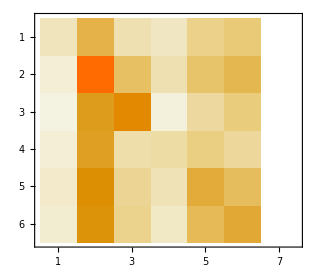

```mathematica
MatrixPlot[{{22,345,39,21,113,152,0},{11,2079,263,39,257,293,0},{1,628,1028,3,78,135,0},{11,612,60,66,134,83,0},{17,796,98,35,450,282,0},{15,795,101,20,283,455,0}}]
```

```mathematica
model =Classify[training->trainLabel,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[model,testing->testLabel]
```

ClassifierMeasurementsObject[…]

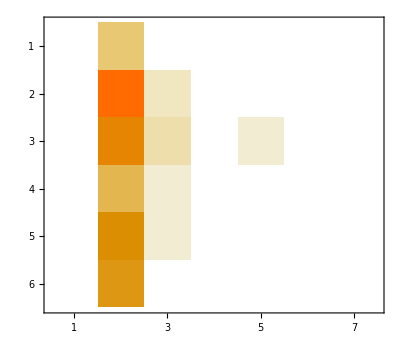

```mathematica
MatrixPlot[cm["ConfusionMatrix"]]
```

```mathematica
model =Classify[training->trainLabel,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[model,testing->testLabel]
```

ClassifierMeasurementsObject[…]

```mathematica
ClassifierInformation[model]
```

Classifier information
Method | Neural network
Number of classes | 6
Number of features | 1
Number of training examples | 88380
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,2727
Hidden layer activation functions | ,,Rectified LinearRectified Linear
CostFunction | Cost Function

```mathematica
fe = FeatureExtraction[training]
```

FeatureExtractorFunction[…]

```mathematica
DATA[[4]][[1]]
```

trainLabel

```mathematica
model =Classify[training->trainLabel,Method->"SupportVectorMachine"]
```